## Hexi — PS 7 — 2025-02-11

## EIWL3 Sections 18 and 19

## I had repeated issues with timeouts when downloading GeoGraphics. Because of that, I did not re-execute your PS7 notebooks like I usually do (to check for errors upon re-execution). Instead, I just PDF’d them the way that you gave them to me.

### Exercises from EIWL3 Section 18

```mathematica
GeoDistance[Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"London","GreaterLondon","UnitedKingdom"}]]
```

3453.71 mi

```mathematica
GeoDistance[Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"London","GreaterLondon","UnitedKingdom"}]]/GeoDistance[Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"SanFrancisco","California","UnitedStates"}]]
```

1.35109

```mathematica
UnitConvert[GeoDistance[Entity["City",{"Sydney","NewSouthWales","Australia"}],Entity["City",{"Moscow","Moscow","Russia"}]],Quantity[, "Kilometers"]]
```

14387. km

```mathematica
GeoGraphics[Entity["Country","UnitedStates"]]
```

-Graphics-

```mathematica
GeoListPlot[{Entity["Country","Brazil"], Entity["Country","Russia"],Entity["Country","India"], Entity["Country","China"]}]
```

-Graphics-

```mathematica
GeoGraphics[GeoPath[{Entity["City",{"NewYork","NewYork","UnitedStates"}], Entity["City",{"Beijing","Beijing","China"}]}]]
```

-Graphics-

```mathematica
GeoGraphics[GeoDisk[Entity["Building","GreatPyramidOfGiza::jbm66"],10 Quantity[, "Miles"]]]
```

-Graphics-

```mathematica
GeoGraphics[GeoDisk[Entity["City",{"NewYork","NewYork","UnitedStates"}],GeoDistance[{Entity["City",{"NewYork","NewYork","UnitedStates"}], Entity["City",{"SanFrancisco","California","UnitedStates"}]}]]]
```

-Graphics-

```mathematica
GeoImage[GeoDisk[Entity["Building","ThePentagon::qzh8d"],0.4 Quantity[, "Miles"]]]
```

-Graphics-

```mathematica
GeoNearest["Country",GeoPosition["NorthPole"],5]
```

{Greenland,Canada,Russia,Svalbard,United States}

{Greenland,Canada,Russia,Svalbard,United States}


{-Graphics-,-Graphics-,-Graphics-}

```mathematica
EntityValue[GeoNearest["Country",{45,0},3],"Flag"]
```

```mathematica
GeoListPlot[GeoNearest["Volcano",Entity["City",{"Rome","Lazio","Italy"}],25]]
```

-Graphics-

```mathematica
Latitude[Entity["City",{"NewYork","NewYork","UnitedStates"}]]-Latitude[Entity["City",{"LosAngeles","California","UnitedStates"}]]
```

6.64488 °

### Exercises from EIWL3 Section 18

```mathematica
Now-DateObject[{1900,1,1},"Day"]
```

45696. days

45696. days

```mathematica
DayName[DateObject[{2000,1,1},"Day"]]
```

Saturday

Saturday

```mathematica
Today-100000 Quantity[, "Days"]
```

Wed 28 Apr 1751

Wed 28 Apr 1751

```mathematica
LocalTime[Entity["City",{"Delhi","Delhi","India"}]]
```

February 11, 2025 3:20 amGMT+5.5

February 11, 2025 3:20 amGMT+5.5

```mathematica
Sunset[Here,Today]-Sunrise[Here,Today]
```

10.0676 h

```mathematica
MoonPhase[Now,"Icon"]
```

-Graphics-

```mathematica
Table[MoonPhase[x],{x,DateObject[{2025,2,10},"Day"],DateObject[{2025,2,20},"Day"],1 Quantity[, "Days"]}]
```

{0.941191,0.980275,0.998115,0.99507,0.972393,0.931991,0.876155,0.807337,0.727997,0.640555,0.547426}

```mathematica
Table[MoonPhase[x,"Icon"],{x,DateObject[{2025,2,11},"Day"],DateObject[{2025,2,20},"Day"],1 Quantity[, "Days"]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Sunrise[Entity["City",{"London","GreaterLondon","UnitedKingdom"}],Today]-Sunrise[Entity["City",{"NewYork","NewYork","UnitedStates"}],Today]
```

-4.53767 h

```mathematica
UnitConvert[Today-DateObject[Entity["MannedSpaceMission","Apollo11"][EntityProperty["MannedSpaceMission","LunarLandingDate"]]],Quantity[, "Years"]]
```

20293/365 yr

```mathematica
AirTemperatureData[Entity["Building","EiffelTower::5h9w8"],DateObject[{2025,2,9,12,0,0},"Instant","Gregorian",-6.]]
```

42.8 °F

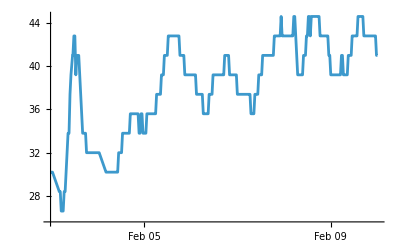

```mathematica
ListLinePlot[AirTemperatureData[Entity["Building","EiffelTower::5h9w8"],{DateObject[{2025,2,3},"Day"],Today}]]
```

```mathematica
AirTemperatureData[Entity["City",{"NewYork","NewYork","UnitedStates"}],Now]-AirTemperatureData[Entity["City",{"LosAngeles","California","UnitedStates"}],Now]
```

-23.9 _Δ^◦F

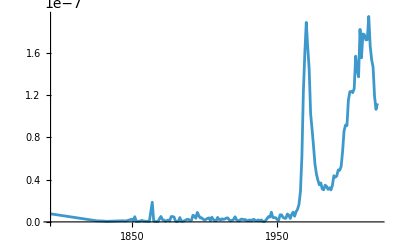

```mathematica
ListLinePlot[WordFrequencyData["groovy","TimeSeries"]]
```

```mathematica
Entity["Country","UnitedKingdom"][Dated["Population",2000]]-Entity["Country","UnitedKingdom"][Dated["Population",1900]]
```

20759628 people